# GHZ STATES - Cirq Amplitude damping

6000 shots

## N = 5 Amplitude Damping

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
N[Subscript[list, th]]
```

{1.,0.0669873,0.75,0.5,0.25,0.933013,0.,0.933013,0.25,0.5,0.75,0.0669873}

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

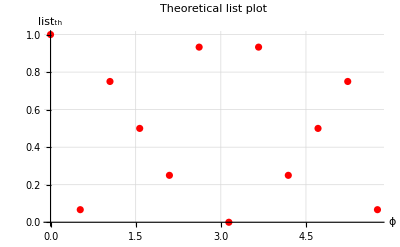

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

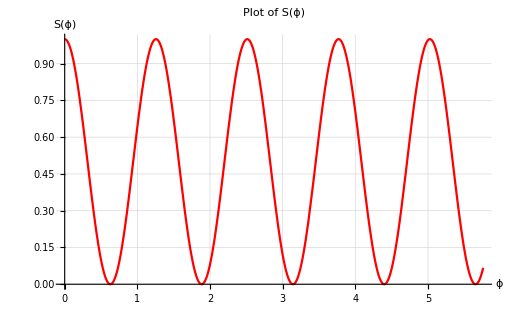

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

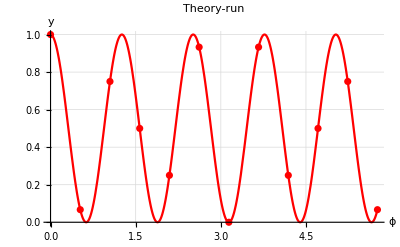

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

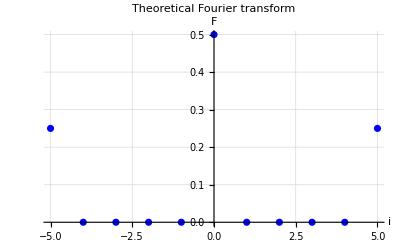

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN NOISE MODEL

1000 shots

```mathematica
data1={1.0,0.06483333333333333,0.745,0.49916666666666665,0.253,0.9313333333333333,0.0,0.9346666666666666,0.25016666666666665,0.491,0.754,0.06483333333333333}; (*γ=0.000125*)
data2={0.872,0.07466666666666666,0.655,0.4505,0.23316666666666666,0.8221666666666666,0.019166666666666665,0.8071666666666666,0.23416666666666666,0.44666666666666666,0.6548333333333333,0.07616666666666666}; (*γ=0.00025*)
data3 = {0.7598333333333334,0.095,0.589,0.4111666666666667,0.22433333333333333,0.7195,0.0475,0.7213333333333333,0.2175,0.39649999999999996,0.588,0.09383333333333332};  (*γ=0.000375*)
data4={0.69,0.1105,0.5303333333333333,0.37366666666666665,0.22949999999999998,0.6346666666666666,0.07333333333333333,0.6555,0.22966666666666666,0.3878333333333333,0.523,0.11533333333333333};  (*γ=0.0005*)

data5={0.6243333333333333,0.1435,0.4968333333333333,0.371,0.22466666666666665,0.5925,0.1075,0.6034999999999999,0.24466666666666667,0.368,0.5003333333333333,0.14483333333333334};  (*γ=0.000625*)
data6 = {0.571,0.16216666666666665,0.45566666666666666,0.3511666666666667,0.24766666666666665,0.5501666666666667,0.13483333333333333,0.5435,0.24333333333333332,0.35683333333333334,0.4695,0.16966666666666666}; (*γ=0.00075*)
data7={0.5373333333333333,0.191,0.422,0.35283333333333333,0.2538333333333333,0.5191666666666667,0.16716666666666666,0.5048333333333334,0.2573333333333333,0.3491666666666667,0.4495,0.19416666666666665}; (*γ=0.000875*)

data8={0.493,0.21333333333333332,0.43116666666666664,0.3466666666666667,0.27416666666666667,0.4731666666666666,0.19649999999999998,0.482,0.27616666666666667,0.35516666666666663,0.43366666666666664,0.21216666666666667};  (*γ=0.001*)
data9={0.489,0.242,0.42,0.359,0.2901666666666667,0.4656666666666667,0.22833333333333333,0.4668333333333333,0.29216666666666663,0.36133333333333334,0.41666666666666663,0.2495};  (*γ=0.00225*)

data10={0.4815,0.269,0.42016666666666663,0.37566666666666665,0.30516666666666664,0.46499999999999997,0.24333333333333332,0.46416666666666667,0.30616666666666664,0.3738333333333333,0.4145,0.271};  (*γ=0.0035*)

data11={0.4716666666666667,0.2885,0.42233333333333334,0.375,0.32866666666666666,0.44766666666666666,0.2791666666666667,0.45249999999999996,0.32575,0.3680833333333333,0.41625,0.29316666666666663};  (*γ=0.00475*)
data12={0.46166666666666667,0.316,0.4240833333333333,0.3824166666666666,0.3478333333333333,0.44408333333333333,0.3123333333333333,0.45825,0.34091666666666665,0.3794166666666667,0.41841666666666666,0.31266666666666665};  (*γ=0.006*)

data13={0.4568333333333333,0.3333333333333333,0.424,0.39349999999999996,0.36683333333333334,0.451,0.33025,0.447,0.36424999999999996,0.38616666666666666,0.42624999999999996,0.33766666666666667};  (*γ=0.001625*)


data14={0.47683333333333333,0.176,0.3953333333333333,0.3183333333333333,0.22999999999999998,0.43466666666666665,0.1545,0.4428333333333333,0.2395,0.30933333333333335,0.39166666666666666,0.17366666666666666};  (*γ=0.002875*)
data15={0.3948333333333333,0.22916666666666666,0.34983333333333333,0.3135,0.2613333333333333,0.3765,0.2135,0.389,0.26116666666666666,0.3025,0.35483333333333333,0.22266666666666665};  (*γ=0.004125*)
data16={0.35733333333333334,0.2798333333333333,0.3478333333333333,0.31466666666666665,0.2886666666666667,0.37416666666666665,0.2543333333333333,0.35183333333333333,0.29166666666666663,0.3148333333333333,0.35383333333333333,0.262};  (*γ=0.005375*)
data17={0.6601666666666667,0.10016666666666667,0.5061666666666667,0.3765,0.21233333333333332,0.6093333333333333,0.06533333333333333,0.62,0.211,0.35783333333333334,0.511,0.10583333333333333};  (*γ=0.0013125*)
```

#### Plot of the data chosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{1.,0.0648333,0.745,0.499167,0.253,0.931333,0.,0.934667,0.250167,0.491,0.754,0.0648333}

12

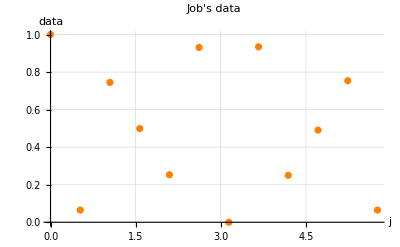

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

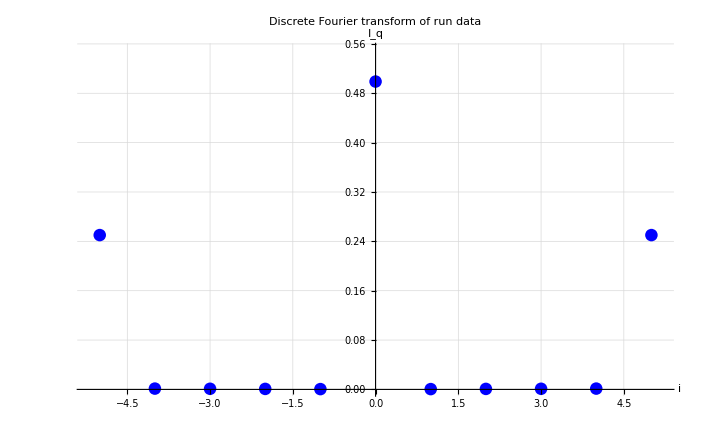

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data4[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data5[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data6[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data7[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data8[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data9[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F10=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data10[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F11=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data11[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F12=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data12[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F13=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data13[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F14=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data14[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F15=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data15[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F16=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data16[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F17=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data17[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]];
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]];
F5Lower2= 2 √F2[[Length[F2]]];
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]];
F5Lower3= 2 √F3[[Length[F3]]];
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]];
F5Lower4= 2 √F4[[Length[F4]]];
F5Upper4=√(F4[[n+1]]/2)+√F4[[Length[F4]]];
F5Lower5= 2 √F5[[Length[F5]]];
F5Upper5=√(F5[[n+1]]/2)+√F5[[Length[F5]]];
F5Lower6= 2 √F6[[Length[F6]]];
F5Upper6=√(F6[[n+1]]/2)+√F6[[Length[F6]]];
F5Lower7= 2 √F7[[Length[F7]]];
F5Upper7=√(F7[[n+1]]/2)+√F7[[Length[F7]]];
F5Lower8= 2 √F8[[Length[F8]]];
F5Upper8=√(F8[[n+1]]/2)+√F8[[Length[F8]]];
F5Lower9= 2 √F9[[Length[F9]]];
F5Upper9=√(F9[[n+1]]/2)+√F9[[Length[F9]]];
F5Lower10= 2 √F10[[Length[F10]]];
F5Upper10=√(F10[[n+1]]/2)+√F10[[Length[F10]]];
F5Lower11= 2 √F11[[Length[F11]]];
F5Upper11=√(F11[[n+1]]/2)+√F11[[Length[F11]]];
F5Lower12= 2 √F12[[Length[F12]]];
F5Upper12=√(F12[[n+1]]/2)+√F12[[Length[F12]]];
F5Lower13= 2 √F13[[Length[F13]]];
F5Upper13=√(F13[[n+1]]/2)+√F13[[Length[F13]]];
F5Lower14= 2 √F14[[Length[F14]]];
F5Upper14=√(F14[[n+1]]/2)+√F14[[Length[F14]]];
F5Lower15= 2 √F15[[Length[F15]]];
F5Upper15=√(F15[[n+1]]/2)+√F15[[Length[F15]]];
F5Lower16= 2 √F16[[Length[F16]]];
F5Upper16=√(F16[[n+1]]/2)+√F16[[Length[F16]]];
F5Lower17= 2 √F17[[Length[F17]]];
F5Upper17=√(F17[[n+1]]/2)+√F17[[Length[F17]]];
```

Fidelity plot

```mathematica
V5Lower={F5Lower1,F5Lower2,F5Lower3,F5Lower4,F5Lower5,F5Lower6,F5Lower7,F5Lower8,F5Lower9,F5Lower10,F5Lower11,F5Lower12,F5Lower13};
V5Upper={F5Upper1,F5Upper2,F5Upper3,F5Upper4,F5Upper5,F5Upper6,F5Upper7,F5Upper8,F5Upper9,F5Upper10,F5Upper11,F5Upper12,F5Upper13};
gamma={0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12};

Lower=Thread[{gamma,V5Lower}];
Upper=Thread[{gamma,V5Upper}];
k=0.125
retta=Plot[0.5,{x,0,k},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

0.125

```mathematica
verticalSize=430;
orSize=600;
```

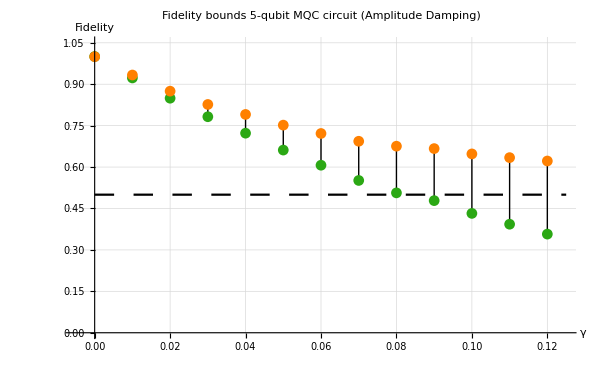

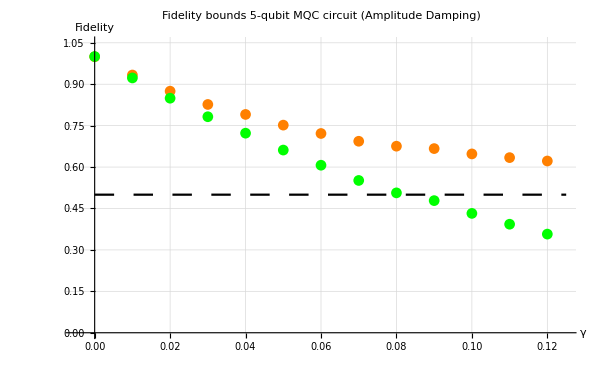

```mathematica
P5L=ListPlot[Lower,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds 5-qubit MQC circuit (Amplitude damping)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.005,k},{0,1.05}}, PlotLegends->{},PlotStyle->{Green},ImageSize->{orSize,verticalSize}];

P5U=ListPlot[Upper,AxesLabel->{HoldForm["γ"],HoldForm["Fidelity"]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{-0.005,k},{0,1.05}}, PlotLegends->{},PlotStyle->{Orange},ImageSize->{orSize,verticalSize},PlotLabel->HoldForm["Fidelity bounds 5-qubit MQC circuit (Amplitude damping)"]];

salvare=ListPlot[{Thread[{gamma,V5Lower}],Thread[{gamma,V5Upper}]},Filling->{1->{2}},FillingStyle->{Black},PlotStyle->{RGBColor[0.17,0.66,0.08],Orange},AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->20],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->20]},PlotLabel->HoldForm["Fidelity bounds 5-qubit MQC circuit (Amplitude Damping)"],LabelStyle->{FontFamily->"Calibri",16,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic ,  PlotRange->{{-0.005,k},{0,1.05}}, PlotLegends->{},ImageSize->{orSize,verticalSize}];
Show[salvare,retta]

a=Show[P5U,retta,P5L,AxesLabel->{ Style["γ",Black,FontFamily->"HoldForm",FontSize->20],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->20]},LabelStyle->{FontFamily->"Calibri",18,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic ,  PlotRange->{{-0.005,k},{0,1.05}}, PlotLegends->{},PlotStyle->{Orange},PlotLabel->HoldForm["Fidelity bounds 5-qubit MQC circuit (Amplitude Damping)"],ImageSize->{orSize,verticalSize}]
```

```mathematica
parameter=0.08;
deltat=1;
T=(- deltat)/Log[1-parameter]
```

11.9931